```mathematica
data=Import["/Users/francesco/Documents/Arduino/bilancino/speed_control/csv/left_motor.csv"];
time=data[[2;;,1]]*10^-6;
ticks=-data[[2;;,2]];
ref=data[[2;;,3]];
speed=Table[(ticks[[i+1]]-ticks[[i]])/(time[[i+1]]-time[[i]]),{i,1,Length[time]-1}]//N;
w=40;
speedFiltered=MovingAverage[speed,w];
time=time[[w;;-2]];
time=time-time[[1]];
ticks=ticks[[w;;-2]];
ref=ref[[w;;-2]];
```

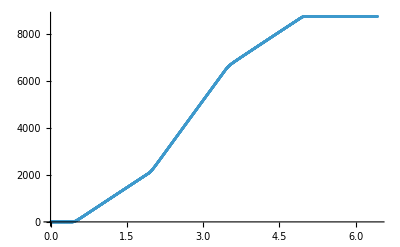

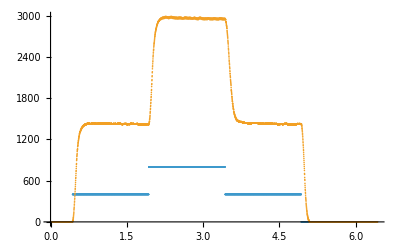

```mathematica
p1=ListPlot[{time,ticks}//Transpose]
p2=ListPlot[{{time,ref}//Transpose,{time,speedFiltered}//Transpose}]
p3=ListPlot[{time,speedFiltered}//Transpose,PlotStyle->{Red}];
```

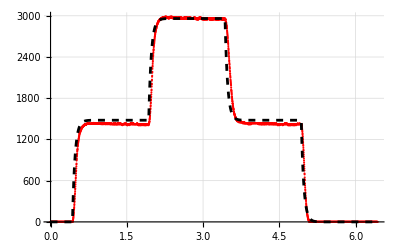

```mathematica
motor=TransferFunctionModel[k/(s+a),s]/.{k->74,a->20}
out=OutputResponse[motor,Interpolation[Transpose[{time,ref}],InterpolationOrder->0][t],{t,time[[1]],time[[-1]]}];
p4=Plot[out,{t,time[[1]],time[[-1]]},PlotStyle->{Dashed,Black}];
Show[{p3,p4},GridLines->Automatic]
```